```mathematica
FindList["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_100.txt", "0\t0\t0"];
```

```mathematica
If[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_100.txt"]=="0\t0\t0", Inicia, Datos];
```

Datos

```mathematica
;
```

```mathematica
ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Mult_Petit.txt"];
```

2	1	2

```mathematica
Do[Print[If[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Mult_Petit.txt"]=="0\t0\t0", Inicia, Datos]], 50];
```

Datos

Datos

Datos

«47 more identical outputs»

```mathematica
arr=Array[#&,  10];
```

{1,2,3,4,5}

```mathematica
str=ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Mult_Petit.txt"];
```

0	13	0

```mathematica
ToExpression[str, TraditionalForm];
```

0

```mathematica
ToExpression[str]
```

0

```mathematica
StringSplit[str]
```

{0,26,0}

```mathematica
ToExpression[StringSplit[str]]
```

{0,26,0}

```mathematica
s=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_100.txt"]]];While[s≠{0, 0,0}, {Print[s], s=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_100.txt"]]]}];
```

{0,7,0}

{0,3,0}

{1,6,0}

{3,7,0}

{5,4,1}

{8,9,0}

{9,4,1}

```mathematica
l={}; k={};Do[{k={}; s=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_100.txt"]]];While[s≠{0, 0,0}, {k=Join[k, {s}], s=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_100.txt"]]]}], l=Join[l, {k}]}, 10]; Print[l]; Length[l[[2]]]
```

{{{0,5,1},{1,9,0},{1,7,1},{1,2,1},{2,7,0},{2,9,1},{2,1,1},{3,4,0},{3,6,1},{4,9,1},{4,1,1},{5,9,1},{5,1,1},{6,9,1},{6,1,1},{7,9,1},{7,1,1},{8,0,1},{9,7,1},{9,2,1}},{{0,7,0},{0,3,0},{1,6,0},{3,7,0},{5,4,1},{8,9,0},{9,4,1}},{{0,2,0},{0,6,1},{1,5,1},{2,6,1},{3,9,0},{3,7,0},{3,2,1},{3,0,1},{4,8,1},{5,2,1},{5,0,1},{7,9,0},{7,5,1},{8,4,1},{9,5,1}},{{3,8,0},{3,7,0},{3,9,1},{3,6,1},{4,5,1},{5,4,1},{6,9,0},{6,4,1},{7,8,0},{7,1,1},{8,4,1},{9,4,1}},{{0,2,0},{0,7,1},{1,7,1},{2,7,1},{3,9,1},{3,6,1},{3,5,1},{3,4,1},{4,9,0},{4,6,0},{4,5,0},{4,1,1},{5,9,0},{5,6,0},{5,7,1},{6,9,0}},{{0,9,0},{0,8,0},{0,4,1},{1,7,1},{1,6,1},{1,2,1},{2,7,0},{2,6,0},{2,9,1},{2,8,1},{2,0,1},{3,7,1},{3,6,1},{3,2,1},{4,5,1},{5,4,1},{6,7,0},{8,9,0},{8,1,1}},{{0,9,0},{0,5,0},{0,6,1},{1,7,1},{4,8,0},{5,9,0},{5,8,1},{5,4,1},{6,1,1}},{{0,2,0},{0,3,1},{1,9,0},{1,2,1},{1,0,1},{2,8,1},{2,4,1},{3,6,1},{4,8,0},{4,3,1},{6,2,1},{6,0,1},{8,7,1},{9,8,1},{9,4,1}},{{1,6,0},{1,3,0},{1,7,1},{2,8,1},{3,6,0},{3,2,1},{4,5,0},{4,8,1},{7,5,1},{7,4,1},{8,6,1},{8,3,1},{8,1,1},{9,0,1}},{{0,1,0},{0,8,1},{3,6,1},{3,4,1},{4,6,0},{5,9,0},{5,7,0},{5,2,1},{6,2,1},{7,9,0},{7,1,1},{7,0,1},{9,1,1},{9,0,1}}}

7

```mathematica
Length[l[[2]]]
```

7

```mathematica
l[[5]]
```

{{0,2,0},{0,7,1},{1,7,1},{2,7,1},{3,9,1},{3,6,1},{3,5,1},{3,4,1},{4,9,0},{4,6,0},{4,5,0},{4,1,1},{5,9,0},{5,6,0},{5,7,1},{6,9,0}}

```mathematica
Length[l[[5]]]
```

16

```mathematica
lista={}; kaux={}; v={}; m=500; n=1000; cc={}; Do[{kaux={}; v={}; cc={}; spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_100.txt"]]];While[spression≠{0, 0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_100.txt"]]]}], t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], cc=ConnectedComponents[Graph[t]], v=VertexDegree[Graph[t]], lista=Join[lista, v], Do[{lista=Join[lista, {0}]}, Evaluate[n-Total[Table[Length[cc[[i]]], {i, 1, Length[cc]}]]]]},m]; bines=HistogramList[lista];h=Table[{Floor[(bines[[1, i]]+bines[[1, i+1]])/2], bines[[2, i]]/(n*m)}, {i, 1, Length[bines[[2]]]}];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
lista2={}; kaux2={}; v2={}; m2=m; n2=n; cc2={}; Do[{kaux2={}; v2={}; cc2={}; spression2=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_010.txt"]]];While[spression2≠{0, 0,0}, {kaux2=Join[kaux2, {spression2}], spression2=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_010.txt"]]]}], t2=Table[kaux2[[i,1]]<->kaux2[[i,2]], {i, 1, Length[kaux2]}], cc2=ConnectedComponents[Graph[t2]], v2=VertexDegree[Graph[t2]], lista2=Join[lista2, v2], Do[{lista2=Join[lista2, {0}]}, Evaluate[n2-Total[Table[Length[cc2[[i]]], {i, 1, Length[cc2]}]]]]},m2]; bines2=HistogramList[lista2];h2=Table[{Floor[(bines2[[1, i]]+bines2[[1, i+1]])/2], bines2[[2, i]]/(n2*m2)}, {i, 1, Length[bines2[[2]]]}];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
lista3={}; kaux3={}; v2={}; m3=m; n3=n; cc3={}; Do[{kaux3={}; v3={}; cc3={}; spression3=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_001.txt"]]];While[spression3≠{0, 0,0}, {kaux3=Join[kaux3, {spression3}], spression3=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Net_001.txt"]]]}], t3=Table[kaux3[[i,1]]<->kaux3[[i,2]], {i, 1, Length[kaux3]}], cc3=ConnectedComponents[Graph[t3]], v3=VertexDegree[Graph[t3]], lista3=Join[lista3, v3], Do[{lista3=Join[lista3, {0}]}, Evaluate[n3-Total[Table[Length[cc3[[i]]], {i, 1, Length[cc3]}]]]]},m3]; bines3=HistogramList[lista3];h3=Table[{Floor[(bines3[[1, i]]+bines3[[1, i+1]])/2], bines3[[2, i]]/(n3*m3)}, {i, 1, Length[bines3[[2]]]}];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
gr1=ListPlot[h, PlotMarkers->Automatic, Joined->True, Mesh->Full, PlotStyle->{PointSize[0.02],Black, Dashed}]; gr2=ListPlot[h2, PlotMarkers->Automatic, Joined->True, Mesh->Full, PlotStyle->{PointSize[0.02],Green, Dashed}]; gr3=ListPlot[h3, PlotMarkers->Automatic, Joined->True, Mesh->Full, PlotStyle->{PointSize[0.02],Red, Dashed}];
```

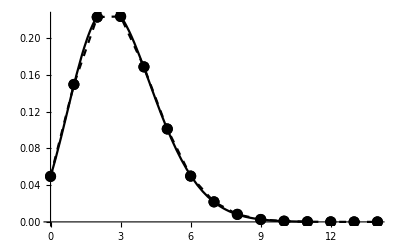

```mathematica
Show[gr1, Plot[Table[PDF[PoissonDistribution[λ],k], {λ, {Mean[lista]}}]//Evaluate, {k, 0, 11}, PlotRange->Automatic, PlotStyle->Black]]
```

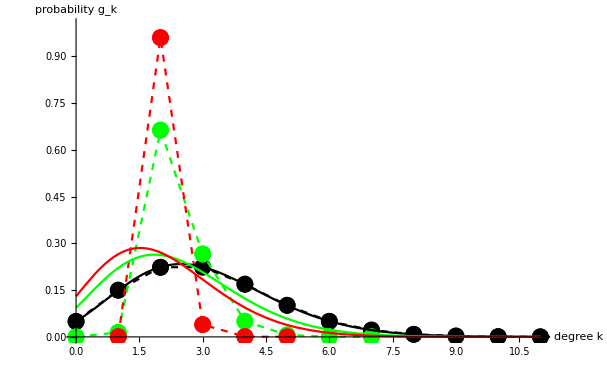

```mathematica
Show[{gr1, gr2, gr3, Plot[Table[PDF[PoissonDistribution[λ],k], {λ, {Mean[lista]}}]//Evaluate, {k, 0, 11}, PlotRange->Automatic, PlotStyle->Black], Plot[Table[PDF[PoissonDistribution[λ],k], {λ, {Mean[lista2]}}]//Evaluate, {k, 0, 11}, PlotRange->Automatic, PlotStyle->Green], Plot[Table[PDF[PoissonDistribution[λ],k], {λ, {Mean[lista3]}}]//Evaluate, {k, 0, 11}, PlotRange->Automatic, PlotStyle->Red]}, PlotRange->{{0,11}, {0,1}}, AxesLabel->{"degree k", "probability g_k"}]
```

```mathematica
N[Mean[lista3]]
```

2.04075

```mathematica
N[150059/50000]
```

3.00118

```mathematica
HistogramList[lista]
```

{{-0.5,0.5,1.5,2.5,3.5,4.5,5.5,6.5,7.5,8.5,9.5,10.5,11.5,12.5,13.5,14.5},{5025,15020,22099,22442,16946,10180,4985,2053,827,288,97,29,6,2,1}}

```mathematica
N[h2]
```

{{0.5,0.00014},{1.5,0.01447},{2.5,0.66084},{3.5,0.26754},{4.5,0.05035},{5.5,0.0063},{6.5,0.00047},{7.5,0.00003}}

```mathematica
TableForm[N[h3]]
```

1. | 0.000454
2. | 0.95947
3. | 0.03949
4. | 0.000838
5. | 0.000016

```mathematica
N[h2]
```

{{0.5,0.00014},{1.5,0.01447},{2.5,0.66084},{3.5,0.26754},{4.5,0.05035},{5.5,0.0063},{6.5,0.00047},{7.5,0.00003}}

```mathematica
lista={}; kaux={}; v={}; m=50; n=100; cc={}; ncc=0; scc={}; x=0; lncc={}; Do[{kaux={}; v={}; cc={}; x=0; spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Petit3.txt"]]];While[spression≠{0, 0,0}, {kaux=Join[kaux, {spression}], spression=ToExpression[StringSplit[ReadLine["F:\\Trabajos\\Estudio\\Fisica\\Escuela\\IB\\Semestre 5\\Tesis\\Net_Generation\\Petit3.txt"]]]}], t=Table[kaux[[i,1]]<->kaux[[i,2]], {i, 1, Length[kaux]}], cc=ConnectedComponents[Graph[t]], v=VertexDegree[Graph[t]], lista=Join[lista, v], x=Evaluate[n-Total[Table[Length[cc[[i]]], {i, 1, Length[cc]}]]],Do[{lista=Join[lista, {0}], cc=Join[cc, {1}]}, x], ncc=Length[cc], lncc=Join[lncc, {ncc}]},m]; bines=HistogramList[lista];binescc=HistogramList[lncc];h=Table[{Floor[(bines[[1, i]]+bines[[1, i+1]])/2], bines[[2, i]]/(n*m)}, {i, 1, Length[bines[[2]]]}];hcc=Table[{Floor[(binescc[[1, i]]+binescc[[1, i+1]])/2], binescc[[2, i]]/Length[lncc]}, {i, 1, Length[binescc[[2]]]}];
```

Part::partw: Part 1 of {} does not exist.

Part::partw: Part 2 of {} does not exist.

```mathematica
lncc
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

{{32,13,65,73,24,17,93,76,15,88,99,71,83,51,75,19,20,40,47,56,21,49,94,84,98,64,41,37,5,36,46,52,58,92,2,11,57,85,35,72,22,78,7,97,69,95,34,18,89,29,80,0,26,55,79,87,60,74,48,12,16,31,86,77,44,62,3,81,9,43,28,96,27,6,59,53,8,54,66,50,14,1,67,33,25,82,91,30,70,10,42,63,4,38,90},{{{0,46,1},{1,10,0},{1,27,1},{2,57,0},{2,40,0},{2,11,0},{3,16,1},{4,82,0},{5,89,0},{5,19,1},{6,33,0},{6,25,0},{6,79,1},{7,97,0},{7,94,0},{7,16,1},{9,81,0},{9,18,0},{11,57,0},{11,40,0},{11,60,1},{12,72,0},{12,96,1},{12,53,1},{13,73,1},{13,24,1},{14,70,1},{16,72,1},{16,12,1},{17,83,0},{17,51,0},{17,13,1},{18,81,0},{18,64,1},{18,41,1},{18,37,1},{19,76,1},{19,56,1},{19,47,1},{19,20,1},{20,76,0},{20,56,0},{20,47,0},{20,92,1},{20,21,1},{21,92,0},{21,15,1},{22,78,0},{22,49,0},{22,86,1},{22,77,1},{22,48,1},{22,44,1},{23,61,0},{24,73,0},{24,99,1},{24,71,1},{25,33,0},{25,63,1},{25,30,1},{26,55,0},{26,52,0},{26,72,1},{26,12,1},{27,67,1},{28,80,0},{29,43,1},{30,63,0},{30,50,1},{31,72,1},{31,12,1},{32,13,1},{34,81,1},{34,18,1},{34,9,1},{36,19,1},{37,64,0},{37,41,0},{37,29,1},{38,91,0},{38,70,1},{40,57,0},{40,76,1},{40,56,1},{40,47,1},{40,20,1},{41,64,0},{41,89,1},{41,5,1},{42,10,1},{42,1,1},{44,86,0},{44,77,0},{44,48,0},{44,31,1},{},{46,19,1},{47,76,0},{47,56,0},{47,85,1},{48,86,0},{48,77,0},{48,85,1},{49,78,0},{49,15,1},{50,16,1},{51,83,0},{51,64,1},{51,41,1},{51,37,1},{52,55,0},{52,19,1},{53,96,0},{53,74,1},{54,86,1},{54,77,1},{54,48,1},{54,44,1},{55,27,1},{56,76,0},{56,35,1},{57,74,1},{58,87,0},{58,19,1},{62,50,1},{64,57,1},{64,40,1},{64,11,1},{64,2,1},{65,32,1},{66,86,1},{66,77,1},{66,48,1},{66,44,1},{67,8,1},{69,95,1},{69,84,1},{71,99,0},{72,92,1},{72,21,1},{73,15,1},{74,8,1},{75,93,1},{76,65,1},{77,86,0},{78,62,1},{79,55,1},{79,52,1},{79,26,1},{80,89,1},{80,5,1},{81,14,1},{82,33,1},{82,25,1},{82,6,1},{84,95,0},{84,88,1},{86,8,1},{87,59,1},{88,73,1},{88,24,1},{89,79,1},{90,63,1},{90,30,1},{91,8,1},{93,13,1},{94,97,0},{94,15,1},{96,0,1},{97,3,1},{98,34,1},{99,98,1}}⟦96,1⟧,{{0,46,1},{1,10,0},{1,27,1},{2,57,0},{2,40,0},{2,11,0},{3,16,1},{4,82,0},{5,89,0},{5,19,1},{6,33,0},{6,25,0},{6,79,1},{7,97,0},{7,94,0},{7,16,1},{9,81,0},{9,18,0},{11,57,0},{11,40,0},{11,60,1},{12,72,0},{12,96,1},{12,53,1},{13,73,1},{13,24,1},{14,70,1},{16,72,1},{16,12,1},{17,83,0},{17,51,0},{17,13,1},{18,81,0},{18,64,1},{18,41,1},{18,37,1},{19,76,1},{19,56,1},{19,47,1},{19,20,1},{20,76,0},{20,56,0},{20,47,0},{20,92,1},{20,21,1},{21,92,0},{21,15,1},{22,78,0},{22,49,0},{22,86,1},{22,77,1},{22,48,1},{22,44,1},{23,61,0},{24,73,0},{24,99,1},{24,71,1},{25,33,0},{25,63,1},{25,30,1},{26,55,0},{26,52,0},{26,72,1},{26,12,1},{27,67,1},{28,80,0},{29,43,1},{30,63,0},{30,50,1},{31,72,1},{31,12,1},{32,13,1},{34,81,1},{34,18,1},{34,9,1},{36,19,1},{37,64,0},{37,41,0},{37,29,1},{38,91,0},{38,70,1},{40,57,0},{40,76,1},{40,56,1},{40,47,1},{40,20,1},{41,64,0},{41,89,1},{41,5,1},{42,10,1},{42,1,1},{44,86,0},{44,77,0},{44,48,0},{44,31,1},{},{46,19,1},{47,76,0},{47,56,0},{47,85,1},{48,86,0},{48,77,0},{48,85,1},{49,78,0},{49,15,1},{50,16,1},{51,83,0},{51,64,1},{51,41,1},{51,37,1},{52,55,0},{52,19,1},{53,96,0},{53,74,1},{54,86,1},{54,77,1},{54,48,1},{54,44,1},{55,27,1},{56,76,0},{56,35,1},{57,74,1},{58,87,0},{58,19,1},{62,50,1},{64,57,1},{64,40,1},{64,11,1},{64,2,1},{65,32,1},{66,86,1},{66,77,1},{66,48,1},{66,44,1},{67,8,1},{69,95,1},{69,84,1},{71,99,0},{72,92,1},{72,21,1},{73,15,1},{74,8,1},{75,93,1},{76,65,1},{77,86,0},{78,62,1},{79,55,1},{79,52,1},{79,26,1},{80,89,1},{80,5,1},{81,14,1},{82,33,1},{82,25,1},{82,6,1},{84,95,0},{84,88,1},{86,8,1},{87,59,1},{88,73,1},{88,24,1},{89,79,1},{90,63,1},{90,30,1},{91,8,1},{93,13,1},{94,97,0},{94,15,1},{96,0,1},{97,3,1},{98,34,1},{99,98,1}}⟦96,2⟧},{23,61}}